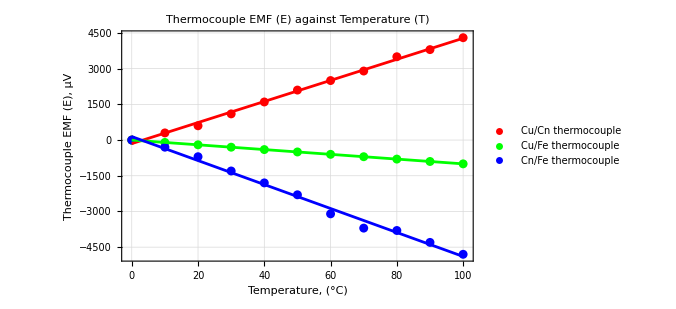
-Graphics-
Cu/Cn thermocouple: y==44.2727 x-150., Uncertainty in Slope: 0.808018
Cu/Fe thermocouple: y==-10. x-1.24345×10^-13, Uncertainty in Slope: 7.45651×10^-16
Cn/Fe thermocouple: y==145.455-50.3636 x, Uncertainty in Slope: 1.55818

```mathematica
(*Define the datasets*)t1={{0,0},{10,300},{20,600},{30,1100},{40,1600},{50,2100},{60,2500},{70,2900},{80,3500},{90,3800},{100,4300}};
t2={{0,0},{10,-100},{20,-200},{30,-300},{40,-400},{50,-500},{60,-600},{70,-700},{80,-800},{90,-900},{100,-1000}};
t3={{0,0},{10,-300},{20,-700},{30,-1300},{40,-1800},{50,-2300},{60,-3100},{70,-3700},{80,-3800},{90,-4300},{100,-4800}};

t1error={
{Around[0,1],Around[0,100]},
{Around[10,1],Around[300,100]},
{Around[20,1],Around[600,100]},
{Around[30,1],Around[1100,100]},
{Around[40,1],Around[1600,100]},
{Around[50,1],Around[2100,100]},
{Around[60,1],Around[2500,100]},
{Around[70,1],Around[2900,100]},
{Around[80,1],Around[3500,100]},
{Around[90,1],Around[3800,100]},
{Around[100,1],Around[4300,100]}};
t2error={
{Around[0,1],Around[0,100]},
{Around[10,1],Around[-100,100]},
{Around[20,1],Around[-200,100]},
{Around[30,1],Around[-300,100]},
{Around[40,1],Around[-400,100]},
{Around[50,1],Around[-500,100]},
{Around[60,1],Around[-600,100]},
{Around[70,1],Around[-700,100]},
{Around[80,1],Around[-800,100]},
{Around[90,1],Around[-900,100]},
{Around[100,1],Around[-1000,100]}};
t3error={
{Around[0,1],Around[0,100]},
{Around[10,1],Around[-300,100]},
{Around[20,1],Around[-700,100]},
{Around[30,1],Around[-1300,100]},
{Around[40,1],Around[-1800,100]},
{Around[50,1],Around[-2300,100]},
{Around[60,1],Around[-3100,100]},
{Around[70,1],Around[-3700,100]},
{Around[80,1],Around[-3800,100]},
{Around[90,1],Around[-4300,100]},
{Around[100,1],Around[-4800,100]}};

(*Fit linear models to the data*)
fitt1=LinearModelFit[t1,x,x];
fitt2=LinearModelFit[t2,x,x];
fitt3=LinearModelFit[t3,x,x];

(*Extracting uncertainties in the slope of each fit*)uncertainty1=fitt1["ParameterTableEntries"][[2,2]];
uncertainty2=fitt2["ParameterTableEntries"][[2,2]];
uncertainty3=fitt3["ParameterTableEntries"][[2,2]];

(*Extract equations as strings*)
eq1=ToString[TraditionalForm[y==fitt1["BestFit"]]];
eq2=ToString[TraditionalForm[y==fitt2["BestFit"]]];
eq3=ToString[TraditionalForm[y==fitt3["BestFit"]]];

(*Existing code for plotting*)Column[{combinedPlot=Show[ListPlot[{t1error,t2error,t3error},PlotStyle->{Red,Green,Blue},PlotLegends->{"Cu/Cn thermocouple","Cu/Fe thermocouple","Cn/Fe thermocouple"}],Plot[{fitt1[x],fitt2[x],fitt3[x]},{x,0,100},PlotStyle->{Red,Green,Blue}],Frame->True,FrameLabel->{"Temperature, (°C)","Thermocouple EMF (E), µV"},GridLines->Automatic,PlotLabel->"Thermocouple EMF (E) against Temperature (T)",ImageSize->500];
(*Displaying the results*)Column[{combinedPlot,Row[{"Cu/Cn thermocouple: ",eq1,", Uncertainty in Slope: ",uncertainty1}],Row[{"Cu/Fe thermocouple: ",eq2,", Uncertainty in Slope: ",uncertainty2}],Row[{"Cn/Fe thermocouple: ",eq3,", Uncertainty in Slope: ",uncertainty3}]}]
}
]
```